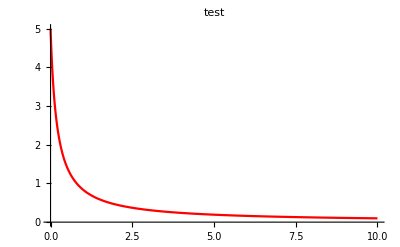

```mathematica
basicTitration1[ktit_,ktat_,concA_,concB_,tmax_:45,title_]:= 
Module[{a,b,c,ab,sol,plotter,rsys},
rsys={
rxn[a+b,ab,ktit],
rxn[a,a+c,ktat],

conc[a,concA],
conc[b,concB]
};
sol=SimulateRxnsys[rsys,tmax];
plotter={a[t]}/.sol;
Show[Plot[plotter,{t,0,tmax},PlotRange->{{0,tmax},{0,5}},PlotStyle->{{Red},{Green}},PlotLabel->title ]]
]
basicTitration1[1,5,5,5,10,"test"]
```

```mathematica
enhancedGRN[k1tx_,k1ctx_,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=
Module[{null,G1,T1,R1,G1c,T1c,C1,sol,rsys},
rsys={
(* Genelet R1 *)
rxn[G1,G1+T1,k1tx],
rxn[T1,T1+R1,ktl],
rxn[T1,null,krd],
rxn[R1,null,kpd],

(* Genelet C1 *)
rxn[G1c,G1c+T1c,k1ctx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

rxn[C1+R1,null,kc],

conc[G1,1],
conc[G1c,1]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{C1[t],R1[t]}/.sol]

]

enhancedGRNPlot[k1tx_,k1ctx_,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=(
plotter=enhancedGRN[k1tx,k1ctx,tmax];
Plot[plotter,{t,0,100},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"R1" ,PlotLegends->{"C1","R1"}])


Directory[]
```

/Users/albert95/Dropbox/Caltech/Jr 15-16/Bi191/b/packages

```mathematica
plot1=Manipulate[enhancedGRNPlot[a,b],{{a,1,"k1tx"},1,500},{{b,250,"k1ctx"},1,500}]
```

ListAnimate[]

plot1.gif

Most of these appear to go to s.s. way before 100s. I’ll just take the lazy approach and take concentrations to be final at 50s.

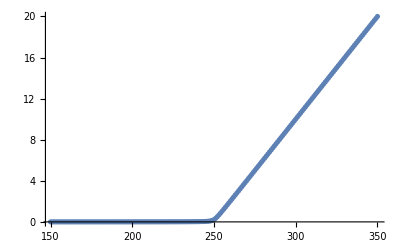

```mathematica
tmax=50;
k1ctx=250;

y=Table[{i,enhancedGRN[i,k1ctx,tmax][[1]][[0]][tmax]},{i,k1ctx-100,k1ctx+100}];
ListPlot[y]
```

```mathematica
enhancedGRN2[k1tx_,k1ctx_,kf_:400,kr_:125,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=
Module[{null,G1,T1,R1,G1c,T1c,C1,sol,rsys,G1f,R1G1f},
rsys={
(* Genelet R1 *)
rxn[G1,G1+T1,k1tx],
rxn[T1,T1+R1,ktl],
rxn[T1,null,krd],
rxn[R1,null,kpd],

(* Genelet C1 *)
rxn[G1c,G1c+T1c,k1ctx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

(* Titration *)
rxn[C1+R1,null,kc],

(* "Reporter" Gene *)
revrxn[R1+G1f,R1G1f,kf,kr],

conc[G1,1],
conc[G1c,1],
conc[G1f,1]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{G1f[t]}/.sol]
]
```

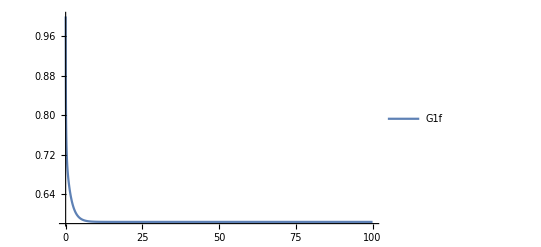

0.58345

```mathematica
plotter=enhancedGRN2[250,250];
Plot[plotter,{t,0,100},PlotRange->All,PlotLegends->{"G1f"}]
plotter[[1]][[0]][100]
```

```mathematica
Do I need to add more things to the system? Let me try to vary the binding rates, to try to get as even error rates, and see if I get anything nice:
```

```mathematica
enhancedGRN2Plot[k1tx_,k1ctx_,kf_:400,kr_:125,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=(
plotter=enhancedGRN2[k1tx,k1ctx,kf,kr,tmax,kc,ktl,kpd,krd];
Plot[plotter,{t,0,100},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"G1f" ])

(* Above the threshold, so manipulating kf will be of particular interest *)
Manipulate[enhancedGRN2Plot[300,250,a,b],{{a,400,"kf"},1,400},{{b,125,"kr"},1,400}]

(* Below the threshold, so manipulating kr will be of particular interest *)
Manipulate[enhancedGRN2Plot[200,250,a,b],{{a,400,"kf"},1,400},{{b,125,"kr"},1,400}]
```

It seems pretty good, but I wonder if I will have to define a metric for what is a “good” error margin. I was thinking along the lines of “are there paramater values for which I can minimize the error for both below and above the threshold” (e.g. trying to minimize the sum of errors?)

Anyways, same thing here: most of these reactions end way before 100s.

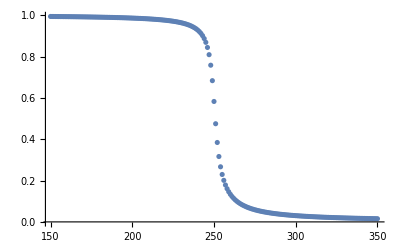

```mathematica
tmax=50;
k1ctx=250;

y=Table[{i,enhancedGRN2[i,k1ctx,400,125,tmax][[1]][[0]][tmax]},{i,k1ctx-100,k1ctx+100}];
ListPlot[y]
```

Really nice. I wonder if computation time will speed up/behavior changes if I scale things down

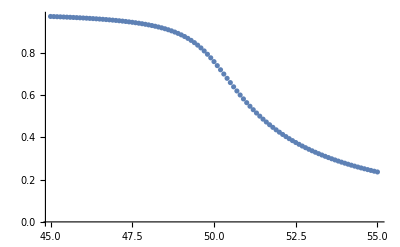

```mathematica
tmax=20;
k1ctx=50;
y=Table[{i,enhancedGRN2[i,k1ctx,40,12.5,tmax][[1]][[0]][tmax]},{i,k1ctx-5,k1ctx+5,0.1}];
ListPlot[y]
```

It seems to get worse if we scale down the rates.

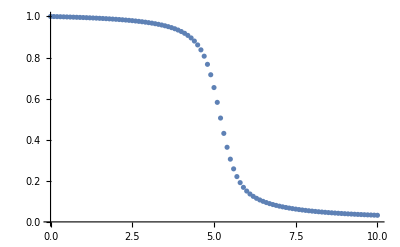

```mathematica
tmax=20;
k1ctx=5;
y=Table[{i,enhancedGRN2[i,k1ctx,1.5,0.05,tmax][[1]][[0]][tmax]},{i,k1ctx-5,k1ctx+5,0.1}];
ListPlot[y]
```

```mathematica
However,changing the relative rates of kf/kr seems to offset part of that. I like saving time, so I may just use these parameters for the future.
```

```mathematica
enhancedGRN3[k1tx_,k1ctx_,kf_:400,kr_:125,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=
Module[{null,G1,T1,R1,G1c,T1c,C1,sol,rsys,G1f,R1G1f},
rsys={
(* Genelet R1 *)
rxn[G1,G1+T1,k1tx],
rxn[T1,T1+R1,ktl],
rxn[T1,null,krd],
rxn[R1,null,kpd],

(* Genelet C1 *)
rxn[G1c,G1c+T1c,k1ctx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

(* Titration *)
rxn[C1+R1,null,kc],

(* "Reporter" Gene *)
revrxn[R1+G1f,R1G1f,kf,kr],

conc[G1,1],
conc[G1c,1],
conc[G1f,10]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{G1f[t]}/.sol]
]

tmax=60;
k1ctx=5;

y=Table[{i,enhancedGRN3[i,k1ctx,1.5,0.05,tmax][[1]][[0]][tmax]},{i,k1ctx-5,k1ctx+5,0.1}];
inv=Interpolation[y];
```

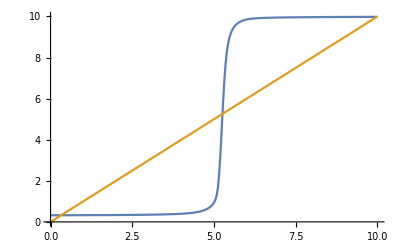

```mathematica
Plot[{inv[inv[x]],x},{x,0,10}]
```

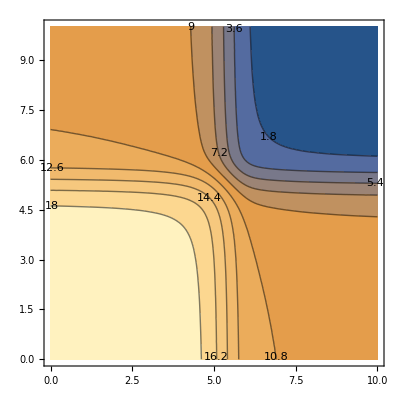

```mathematica
NAND[x_,y_]:=inv[x]+inv[y]
ContourPlot[NAND[x,y],{x,0,10},{y,0,10},ContourLabels->True,Contours->10]
```

```mathematica
Now I'll try to build a function that uses a better steady-state approximation.
```

```mathematica
SS[k1tx_,k1ctx_,kf_:400,kr_:125,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=
If[
```

0.0103087